Module 1: Setting up Hamiltonian for the whole system without PBC
Basis states: |uu...u> , |uu...d>, |u....du>, |u....dd>, ... |dd...d>
Definition of system: [A... cut][(cut+1)..B]. The bond is placed at cut --- cut+1

```mathematica
Timing[
Clear["Global`*"];

n=10; (* No of sites *)
cut=5; (* Where the bond is *)

g=0.5; (* If we want a constant field *) 
glist=Join[Table[g,cut],Table[g,n-cut]]; 
θ=N[π/4]; (* Tilting angle from z axis *)

(* If we want a random field coupling for the spin bath *) 
(* glist=RandomReal[{-1,1},n]; *) 

If[cut<n, 
(
dim=2^n; (* Dimension of Hilbert space *)
Print["Dim of Hilbert space: ",dim];

(* Spin matrices in the many-body Hilbert space *)
Do[
list1=Table[1,2^(n-i)];
If[i>1,list1=PadRight[list1,2^(n-i+1)]];
list2=Table[1,2^(n-i)];
list2=PadRight[list2,2^(n-i+1),-1];

S[i,1]=0.5*SparseArray[{Band[{1,1+2^(n-i)},{dim,dim}]->list1,Band[{1+2^(n-i),1},{dim,dim}]->list1}];
S[i,2]=0.5*SparseArray[{Band[{1,1+2^(n-i)},{dim,dim}]->-ⅈ*list1,Band[{1+2^(n-i),1},{dim,dim}]->ⅈ*list1}];
S[i,3]=0.5*SparseArray[{Band[{1,1},{dim,dim}]->list2}];
,{i,1,n}];

(* I put a non-integrable 1D tilted field Ising model on each side, except on the bond with no field there *)
HA[Ja_,g1_]:=-Ja*Sum[S[i,3].S[i+1,3],{i,1,cut-1}]-Sum[g1[[i]]*Sin[θ]*S[i,1]+g1[[i]]*Cos[θ]*S[i,3],{i,1,cut-1}];
HB[Jb_,g2_]:=-Jb*Sum[S[i,3].S[i+1,3],{i,cut+1,n-1}]-Sum[g2[[i]]*Sin[θ]*S[i,1]+g2[[i]]*Cos[θ]*S[i,3],{i,cut+2,n}];
HAB[Jab_]:=-Jab*(S[cut,3].S[cut+1,3]);
);
];
Clear[list1,list2];
]
```

Dim of Hilbert space: 1024

{0.068228,Null}

Module 2: Check commutation relation: [HA, HAB], [HB,HAB], [HA,HB]
If Max-Min=0, then the commutator is zero

```mathematica
com1=HA[Ja,glist].HAB[Jab]-HAB[Jab].HA[Ja,glist];
com2=HB[Jb,glist].HAB[Jab]-HAB[Jab].HB[Jb,glist];
com3=HA[Ja,glist].HB[Jb,glist]-HB[Jb,glist].HA[Ja,glist];
Max[com1]-Min[com1]//Chop
Max[com2]-Min[com2]//Chop
Max[com3]-Min[com3]//Chop
Clear[com1,com2,com3];
```

0

0

0

Option 1: Setting up the Hamiltonian for the subsystem A and obtain eigenstates

```mathematica
Timing[
nA=cut;
dimA=2^nA; (* Dimension of Hilbert space for A *)

(* Spin matrices in the subsystem Hilbert space *)
Do[
l1=Table[1,2^(nA-i)];
If[i>1,l1=PadRight[l1,2^(nA-i+1)]];

l2=Table[1,2^(nA-i)];
l2=PadRight[l2,2^(nA-i+1),-1];

s[i,1]=0.5*SparseArray[{Band[{1,1+2^(nA-i)},{dimA,dimA}]->l1,Band[{1+2^(nA-i),1},{dimA,dimA}]->l1}];
s[i,2]=0.5*SparseArray[{Band[{1,1+2^(nA-i)},{dimA,dimA}]->ⅈ*l1,Band[{1+2^(nA-i),1},{dimA,dimA}]->-ⅈ*l1}];
s[i,3]=0.5*SparseArray[{Band[{1,1},{dimA,dimA}]->l2}];
,{i,1,nA}];

(* Copy from HA, but need to change the dimension *)
Haaa[Ja_,g1_]:=-Ja*Sum[s[i,3].s[i+1,3],{i,1,nA-1}]-Sum[g1[[i]]*Sin[θ]*s[i,1]+g1[[i]]*Cos[θ]*s[i,3],{i,1,nA-1}];
Clear[l1,l2];
];
```

Option 2: Put a random state for subsystem A (or B as well)

```mathematica
(* General a random complex vector with norm 1 *)
sphericalrandomcomplex[n_]:=Normalize/@(RandomVariate[NormalDistribution[0,1],{1,2^n,2}].{1,I});
ranA=Flatten[sphericalrandomcomplex[nA]];
ranB=Flatten[sphericalrandomcomplex[n-nA]];
ran=Flatten[sphericalrandomcomplex[n]];

(* Check normalization *)
Norm[ranA]
Norm[ranB]
Norm[ran]
```

1.

1.

1.

Module 3: Diagonalize the time-independent Hamiltonian and simulate the dynamics

```mathematica
Timing[
(* Hamiltonian *)
H[Ja_,Jb_,Jab_,g1_,g2_]:=Normal[HA[Ja,g1]+HB[Jb,g2]+HAB[Jab]];

(* Parameters *)
Ja=1.;
Jb=1.;
Jab=0.;
shift=50.; (* To sort the spectrum correctly *)

(* Diagonalize the Hamiltonian for the whole system AxB *)
sol=Eigensystem[H[Ja,Jb,Jab,glist,glist]-shift*IdentityMatrix[dim]];
en=sol[[1]]+shift;
vec=sol[[2]]//Chop;

u=N[{1,0}]; (* spin up *)
d=N[{0,1}]; (* spin down *)
x=N[(u+d)/Sqrt[2]];

solA=Eigensystem[Haaa[Ja,glist]-shift*IdentityMatrix[dimA]];

(* Initial state for A *)

stateA=ranA; 
stateA=solA[[2,1]]; (* This is ground state of HA *) 
stateA=Flatten[KroneckerProduct[x,x,x,x,x]];

stateB=ranB; (* Initial state for B *)

 ψ=Flatten[KroneckerProduct[stateA,stateB]];   (* Initial state for AxB *) 
(*  ψ=ran; (* Fully random states *) *)
]
```

{0.621749,Null}

```mathematica
Print["Spectrum for HA: ",solA[[1]]+shift]
Print["<HA>: ",Conjugate[stateA].Haaa[Ja,glist].stateA//Chop]
```

Spectrum for HA: {-1.81244,-1.36854,-0.951135,-0.921623,-0.661387,-0.622235,-0.533812,-0.519579,-0.43574,-0.414421,-0.307923,-0.223738,-0.180516,-0.101297,-0.00981233,0.00519749,0.0876706,0.11659,0.169865,0.210833,0.284718,0.426423,0.431131,0.477791,0.521422,0.567546,0.656957,0.81708,0.839195,1.04959,1.16155,1.24064}

<HA>: -0.707107

```mathematica
stateA//Chop
```

{0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777}

Module 4: Energy level spacing and entanglement entropy of eigenstate
The algorithm for reduced density matrix and EE work for both pure and mixed states
Note: I use log with base 2 in defining EE. Therefore, EE_max = -N1(1/N1)Log[2, 2^N1] =N1 . Here, N1 is the no of spins in subsystem 1 (not necessarily A)
partition is the location of bi-partitioning the system, not necessarily the same as nA
Module partial trace out anything starting from (partition+1)

```mathematica
SA[Ψ_,partition_]:=(
l1=Table[2,2n];
l2=Table[{j,n+j},{j,partition+1,n}];
l3=Join[{Table[j,{j,1,partition}],Table[j+partition,{j,1,partition}]}];

Clear[ρ,ρA,rhoP,EEA];
ϵ=10^(-12); (* a small number to remove divergence in calculating von Neumann entropy *)

ρ=KroneckerProduct[Ψ,Conjugate[Ψ]];
rhoP=ArrayReshape[ρ,l1];
ρA=TensorContract[rhoP,l2];
ρA=Flatten[ρA,l3];
λ=Eigenvalues[ρA]//Chop;
EEA=-Sum[λ[[j]]*Log[2,λ[[j]]+ϵ],{j,1,2^partition}]//Chop;
);
```

```mathematica
(* Timing[
SAlist=Table[{},n-1];
Do[
Do[
SA[vec[[i]],j];
SAlist[[j]]=Append[SAlist[[j]],{en[[i]],EEA}];,
{i,1,dim}];,
{j,1,n-1}];
] *)

(* Only for half cut to save time *)
Timing[
SAlist={};

Do[
SA[vec[[i]],cut];
SAlist=Append[SAlist,{en[[i]],EEA}];,
{i,1,dim}];
]
```

{12.5172,Null}

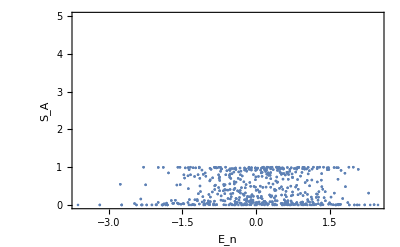

```mathematica
Show[ListPlot[SAlist,PlotRange->Automatic,Frame->True,FrameLabel->{"E_n","S_A"}],PlotRange->{All,{0,cut}},AxesOrigin->{0,0}]
Print["Spectrum for H: ",en]
```

Module 5: von Neumann entropy of each site - Partial tracing out all other spins
Note: I use log with base 2 in defining entropy, so the thermal value is Log(2,2)=1, but not ln 2

```mathematica
vN[Ψ_,k_]:=(
b1=Table[2,2n];
b2=Join[Table[{j,n+j},{j,1,k-1}],Table[{j,n+j},{j,k+1,n}]];

Clear[λ,ρ,ρk,rhoP,vNEE];
ϵ=10^(-12); (* a small number to remove divergence in calculating von Neumann entropy *)

ρ=KroneckerProduct[Ψ,Conjugate[Ψ]];
rhoP=ArrayReshape[ρ,b1];
ρk=TensorContract[rhoP,b2];
ρk=Flatten[ρk,{{1},{2}}];
λ=Eigenvalues[ρk]//Chop;
vnEE=-Sum[λ[[j]]*Log[2,λ[[j]]+ϵ],{j,1,2}]//Chop;
Clear[b1,b2]
);
```

Calculate physical quantities (For longer simulation time, go to 8 sites for gaining insights. Later, go back to 10 sites for better results )

```mathematica
Timing[
end=50000;

comp=Table[Conjugate[vec[[i]]].ψ//Chop,{i,1,dim}]; (* Calculate the components *)
Ψ[t_]:=Sum[Exp[-ⅈ*en[[j]]*t]*comp[[j]]*vec[[j]],{j,1,dim}];

Llist={}; (* Loschmidt echo *)
σlist={}; (* Storing <Sz> at every site *)
vNlist={}; (* Storing vN entropy at every site *)

HAlist1={}; (* Storing <HA> *)
HBlist1={}; (* Storing <HB> *)
HAlist2={}; (* Storing <HA+HAB/2> *)
HBlist2={}; (* Storing <HB+HAB/2> *)
Hlist={};
EEAlist={}; (* Storing EE at half cut *)

Do[
Clear[wav, EEA,vnEE];
wav=Ψ[t];

Llist=Append[Llist,{t,Abs[Conjugate[ψ].wav]^2}];

Do[
σlist=Append[σlist,Conjugate[wav].S[k,3].wav//Chop];
vN[wav,k];
vNlist=Append[vNlist,vnEE]
,{k,1,n}];

HAlist1=Append[HAlist1,{t,Conjugate[wav].HA[Ja,glist].wav//Chop}];
HBlist1=Append[HBlist1,{t,Conjugate[wav].HB[Jb,glist].wav}];
Hlist=Append[Hlist,{t,Conjugate[wav].H[Ja,Jb,Jab,glist,glist].wav}];
HAlist2=Append[HAlist2,{t,Conjugate[wav].(HA[Ja,glist]+HAB[Jab]/2).wav}];
HBlist2=Append[HBlist2,{t,Conjugate[wav].(HB[Jb,glist]+HAB[Jab]/2).wav}];

SA[wav,cut]; 
EEAlist=Append[EEAlist,{t,EEA}];

,{t,0,end,end/500}];

σlist=Partition[σlist,n];
vNlist=Partition[vNlist,n];
]
```

{262.56,Null}

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. 
Completely random state
10 sites, NA=NB=5, JA=JB=JAB=1, g1=0.5, θ=π/4

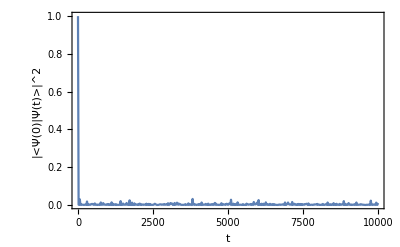

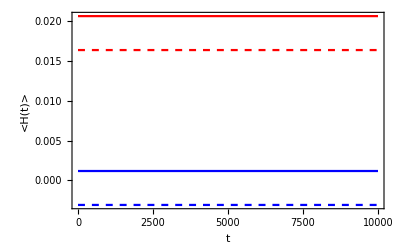

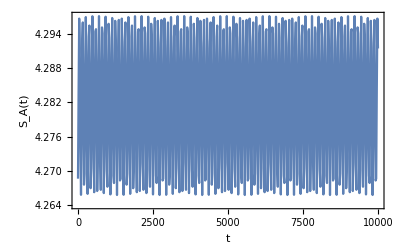

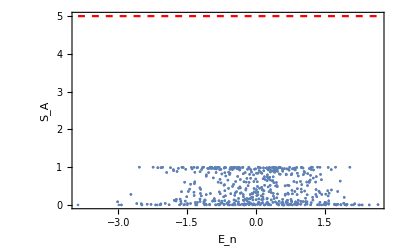

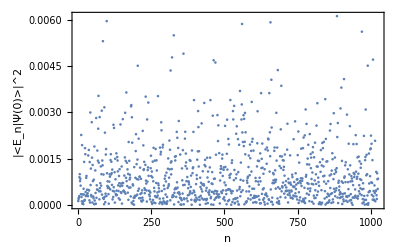

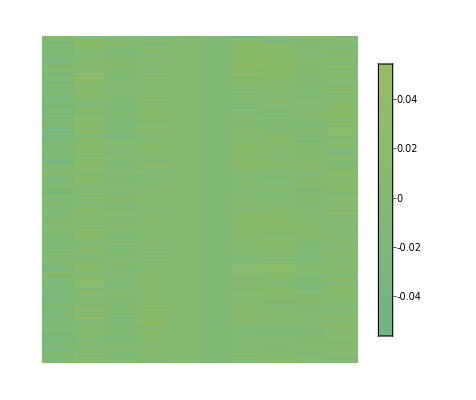

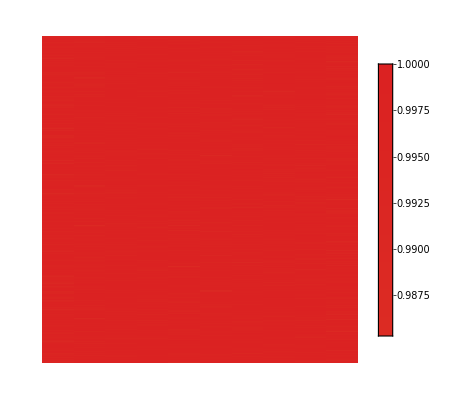

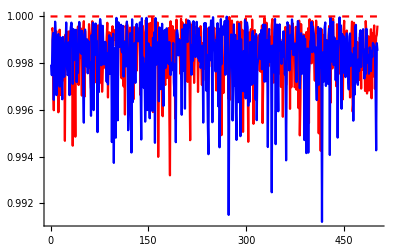

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. A start at the ground state and B start at a random state
10 sites, NA=NB=5, JA=JB=JAB=1, g1=0.5, θ=π/4

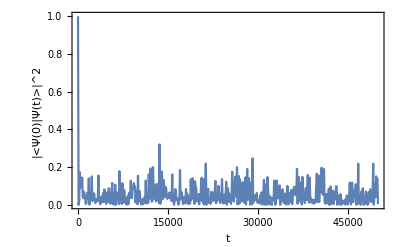

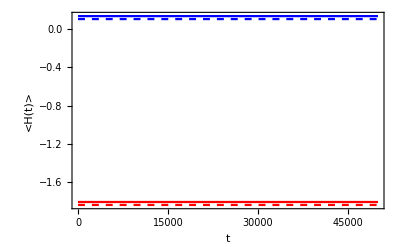

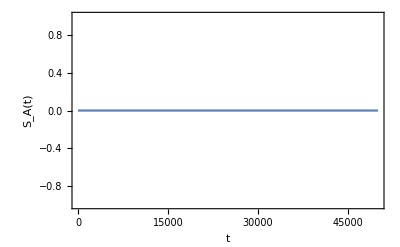

-Graphics-

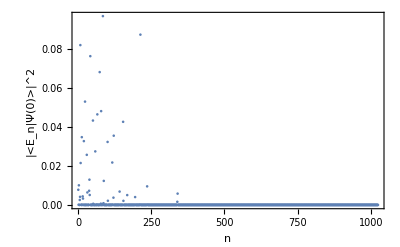

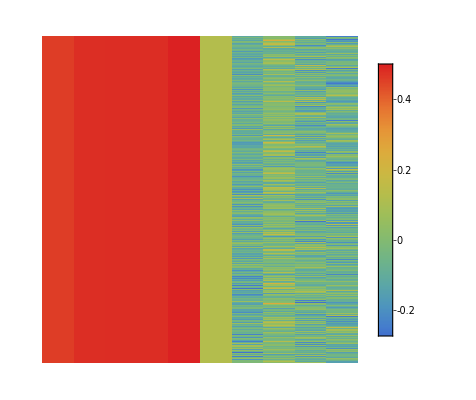

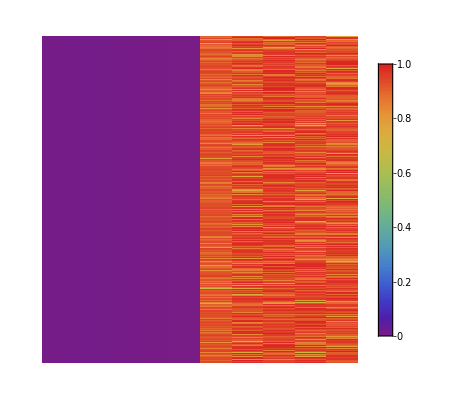

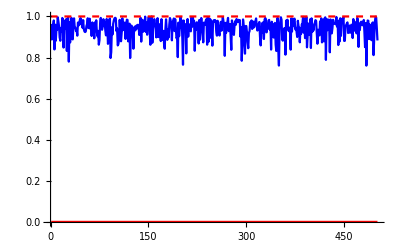

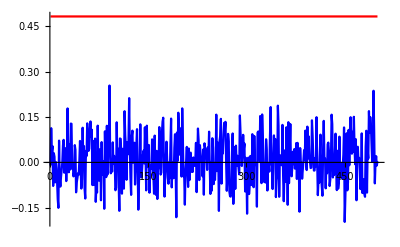

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. A start at |uuuuu> (very low energy) and B start at a random state (middle)
10 sites, NA=NB=5, JA=JB=JAB=1, g1=0.5, θ=π/4
Short time t=200 to see the dynamics

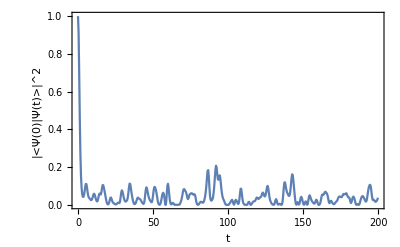

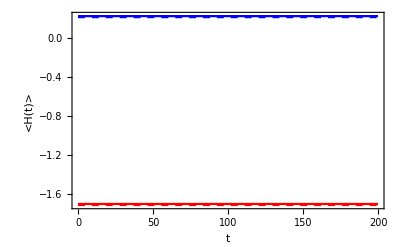

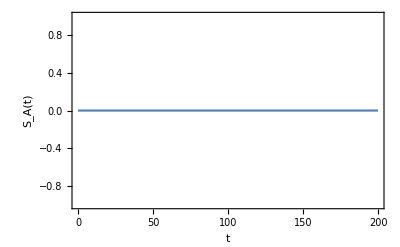

-Graphics-

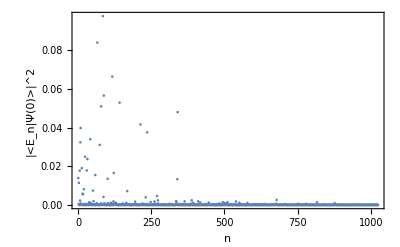

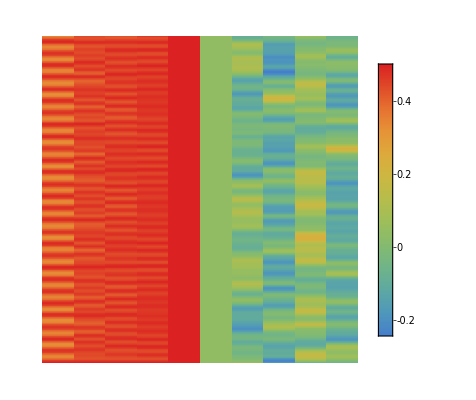

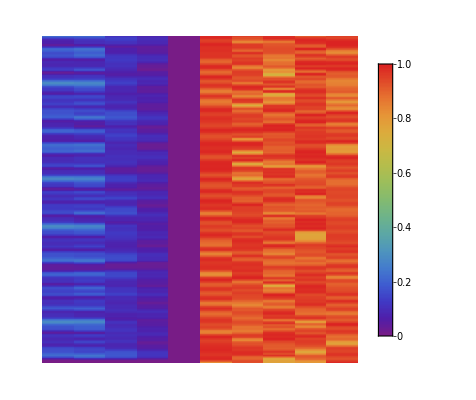

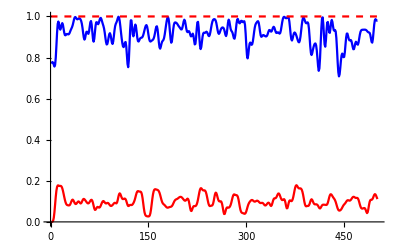

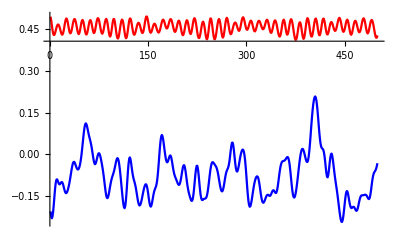

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

p1=ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

p2=ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. A start at |uuuuu> (very low energy) and B start at a random state (middle)
10 sites, NA=NB=5, JA=JB=JAB=1, g1=0.5, θ=π/4
Simulate to t=50000 (thermalized in the generic case) and see if Sz remains high.

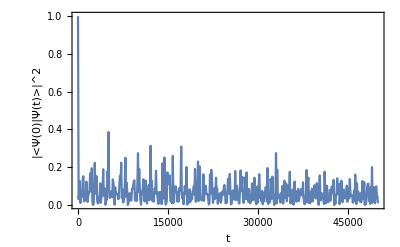

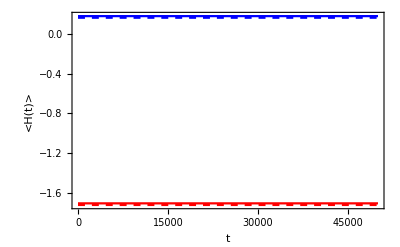

-Graphics-

-Graphics-

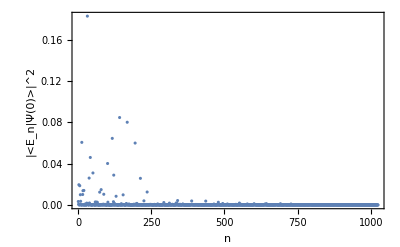

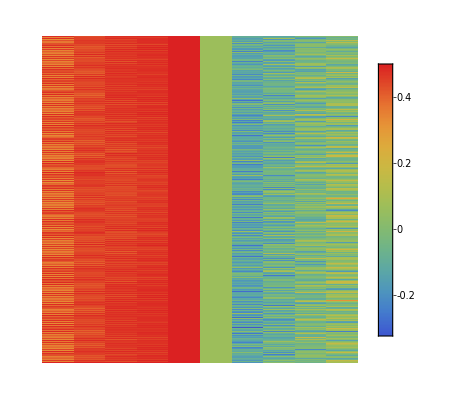

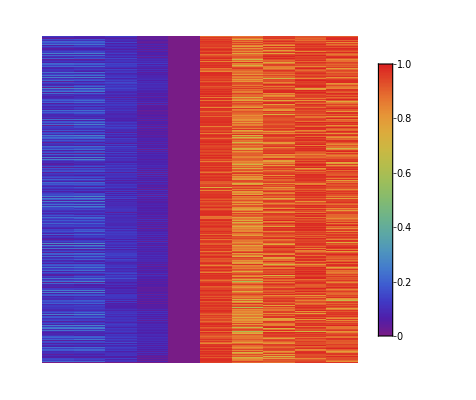

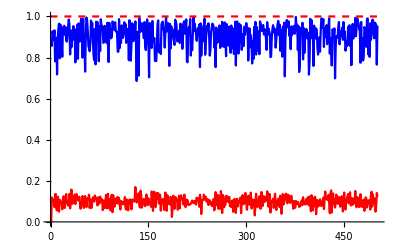

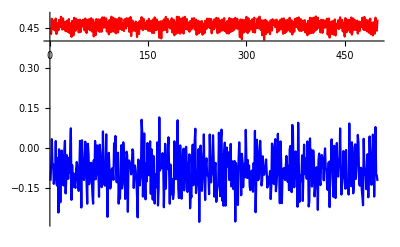

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

p1long=ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

p2long=ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. A start at |xxxxx> (very low energy) and B start at a random state (middle)
10 sites, NA=NB=5, JA=JB=JAB=1, g1=0.5, θ=π/4
Simulate to t=50000 (thermalized in the generic case)
Entropy flows? or just subsystem dynamics on its own?

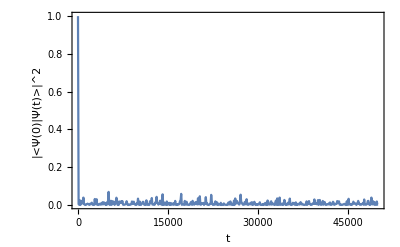

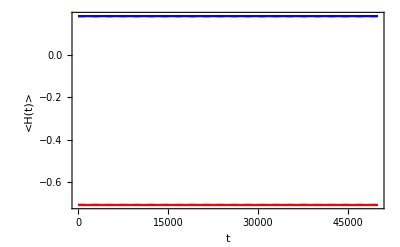

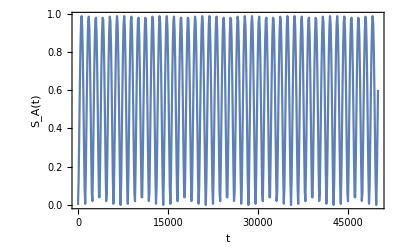

-Graphics-

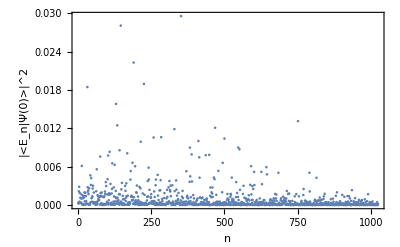

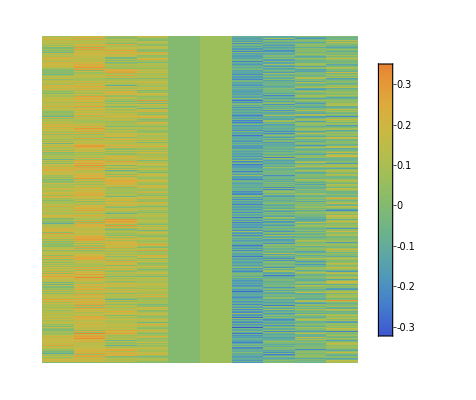

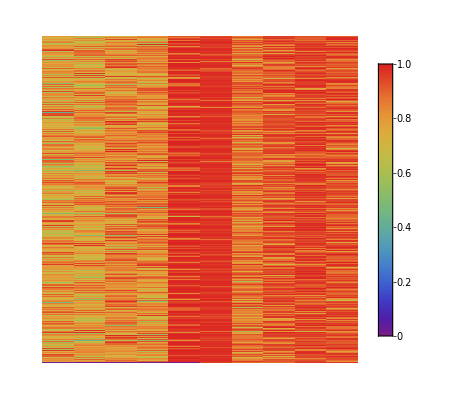

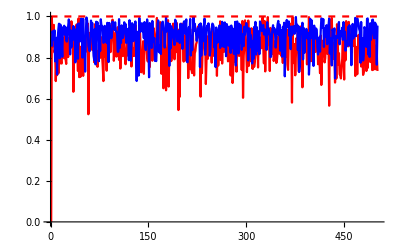

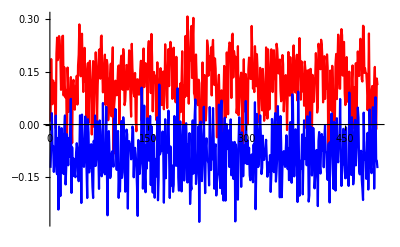

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. A start at |xxxxx> (very low energy) and B start at a random state (middle), Simulate to t=50000 (thermalized in the generic case)
10 sites, NA=NB=5, JA=JB=JAB=0, g1=0.5, θ=π/4
Test whether it is entropy flows or just subsystem dynamics on its own?

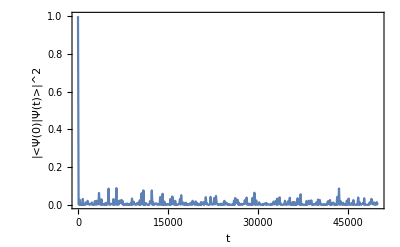

-Graphics-

-Graphics-

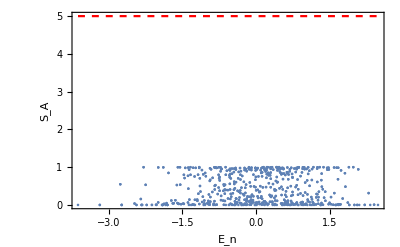

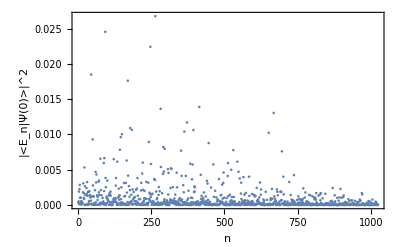

-Graphics-

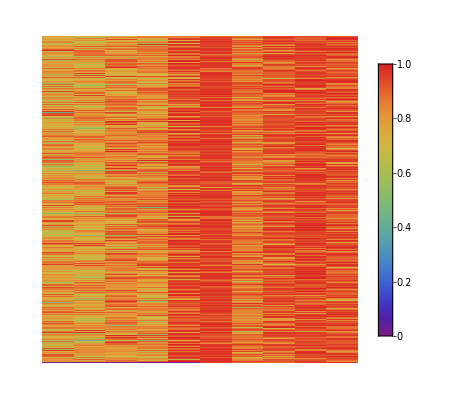

-Graphics-

-Graphics-

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 1: [HA, HAB]=0, [HB, HAB]=0. Both A  and B start at a random state
10 sites, NA=NB=5, JA=JB=JAB=1, g1=0.5, θ=π/4

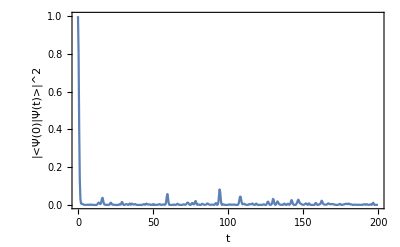

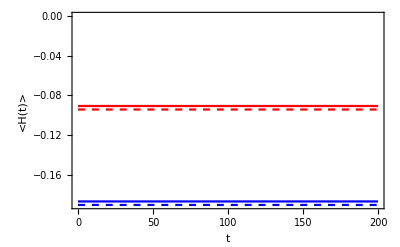

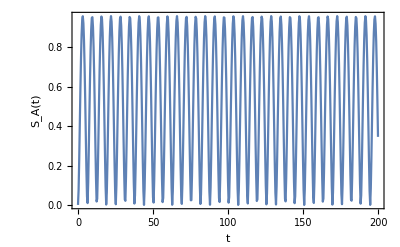

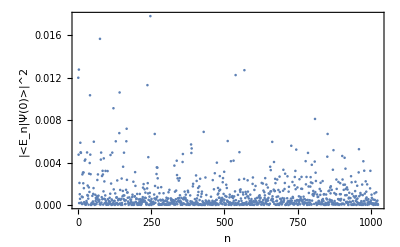

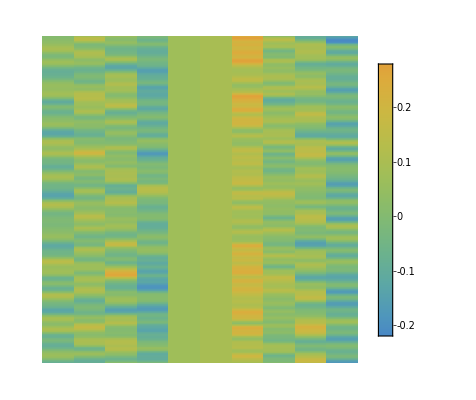

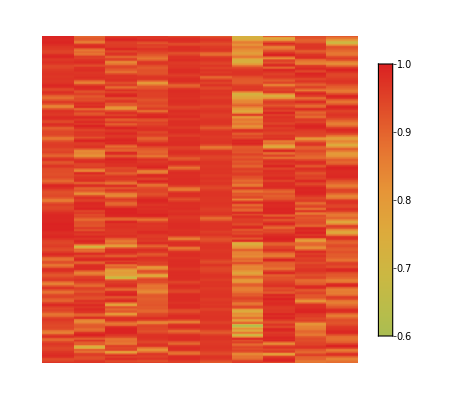

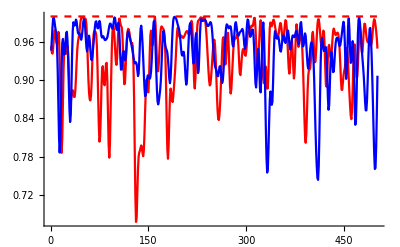

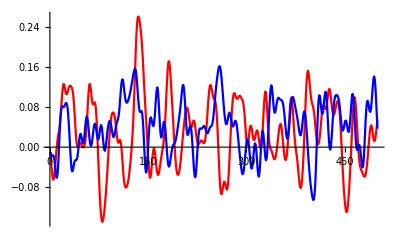

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 2: [HA, HAB]=0, [HB, HAB]!=0. z-x bond
A starts at ground state and B with a random state
10 sites, NA=5, NB=5, JA=JB=JAB=1, g=0.5, θ=π/4

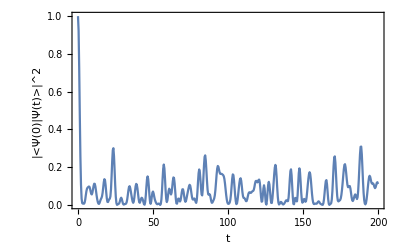

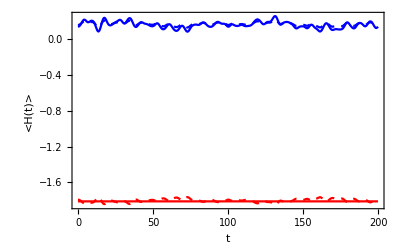

-Graphics-

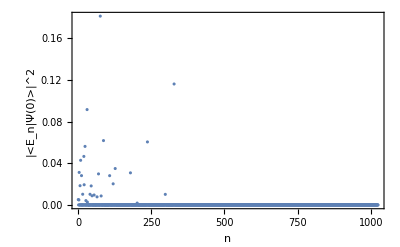

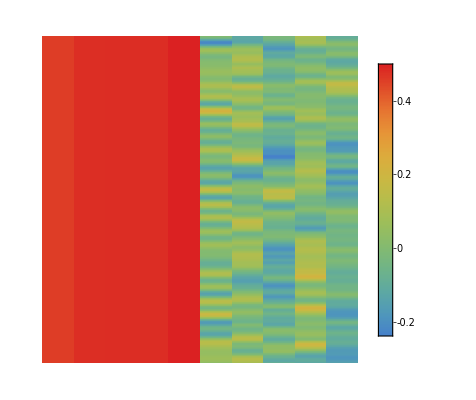

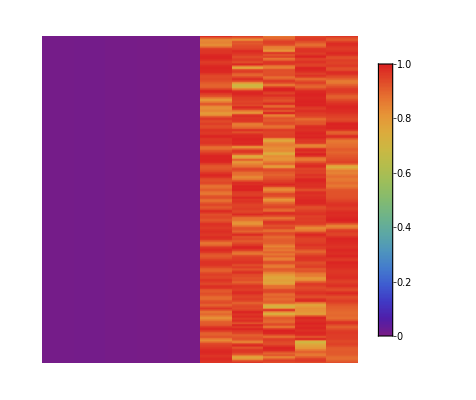

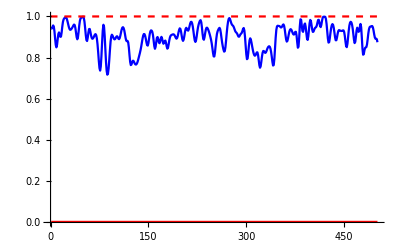

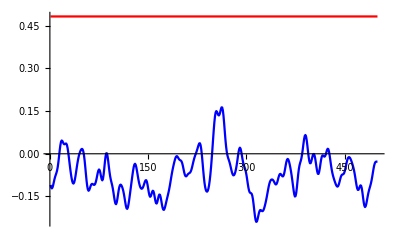

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

Plot for testing the proposal 2: [HA, HAB]=0, [HB, HAB]!=0. z-x bond
A starts at |uuuuu> and B with a random state
10 sites, NA=5, NB=5, JA=JB=JAB=1, g=0.5, θ=π/4
Simulate to t=50000

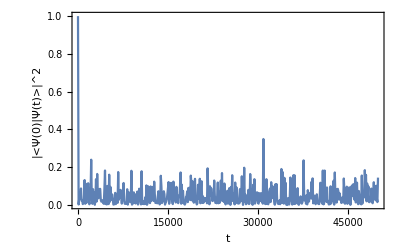

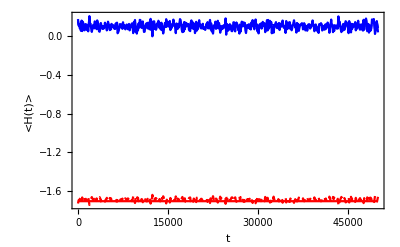

-Graphics-

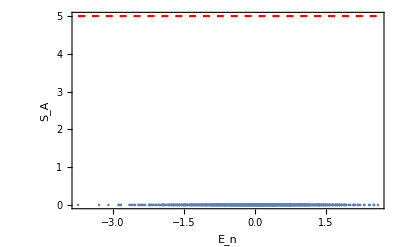

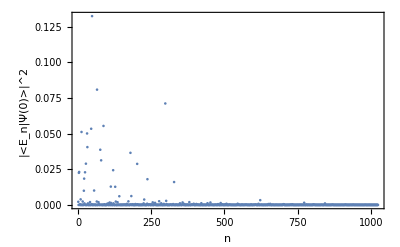

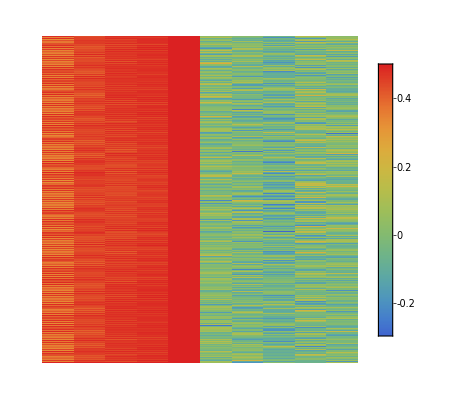

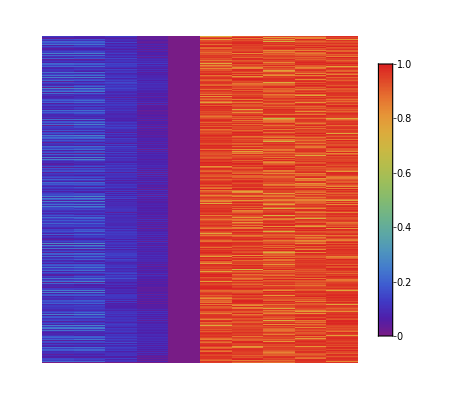

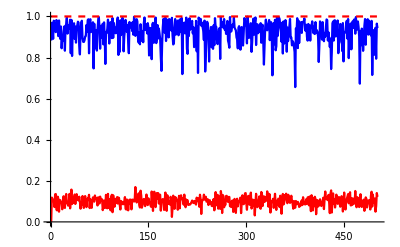

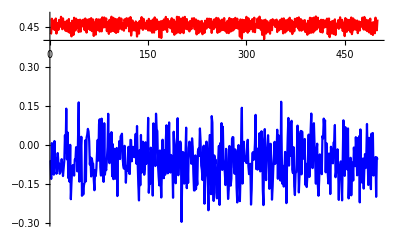

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]
```

```mathematica
Export["sz2.pdf",p3]
Export["vN2.pdf",p4]
```

sz2.pdf

vN2.pdf

Plot for testing the proposal 2: [HA, HAB]=0, [HB, HAB]!=0. z-x bond
A starts at |xxxxx > and B with a random state
10 sites, NA=5, NB=5, JA=JB=JAB=1, g=0.5, θ=π/4

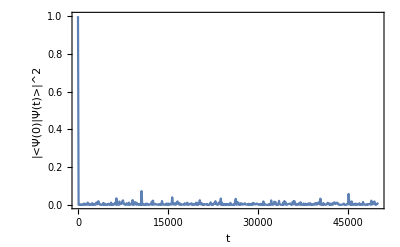

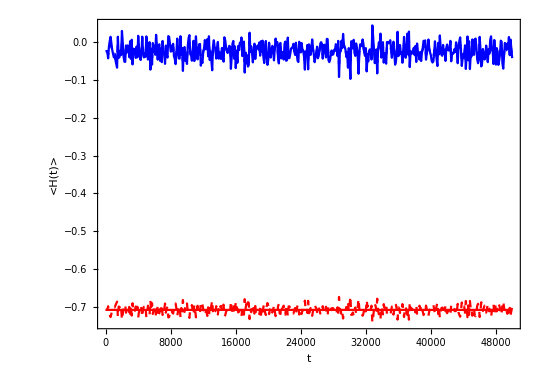

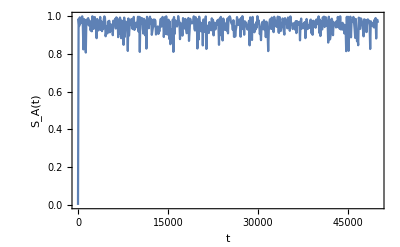

-Graphics-

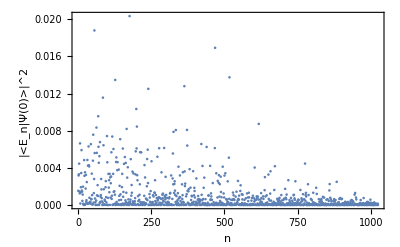

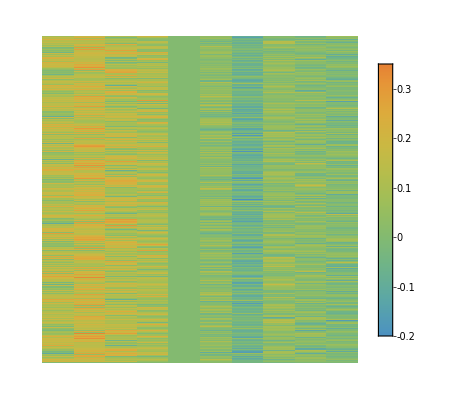

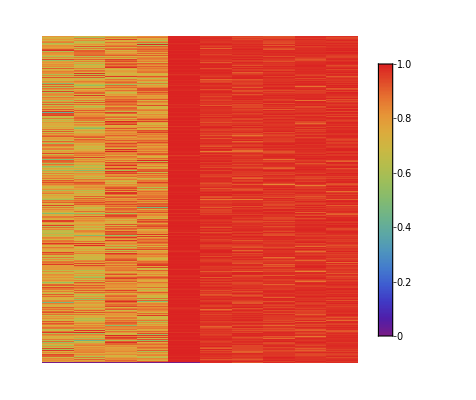

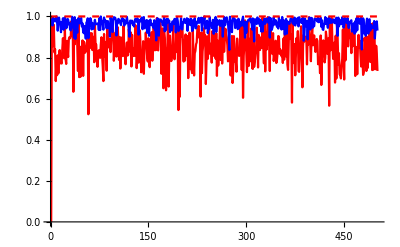

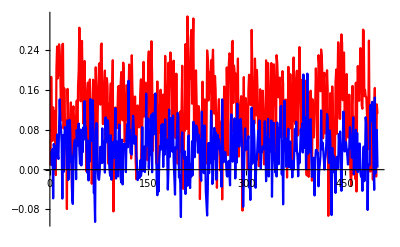

-Graphics-

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]

enexp=Conjugate[ψ].H[Ja,Jb,Jab,glist,glist].ψ//Chop;
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False,Epilog->{HalfLine[{enexp,0},{0,1}]}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
```

Plot for testing the proposal 2: [HA, HAB]=0, [HB, HAB]!=0. Both A and B start with a random state
10 sites, NA=5, NB=5, JA=JB=JAB=1, g=0.1, θ=π/4

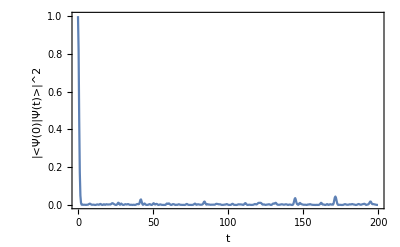

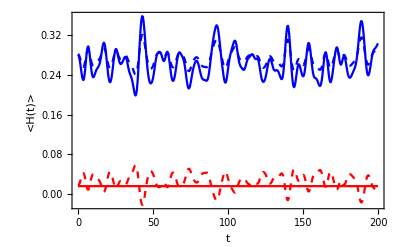

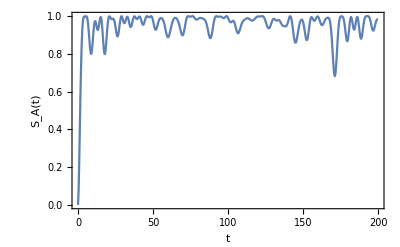

-Graphics-

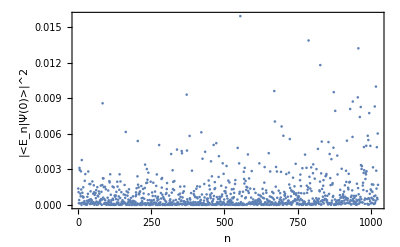

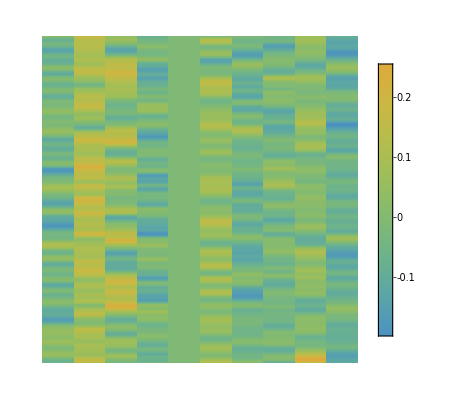

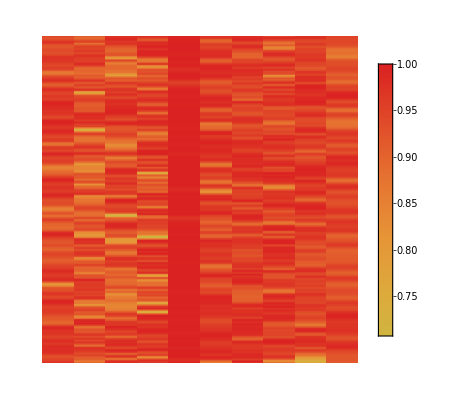

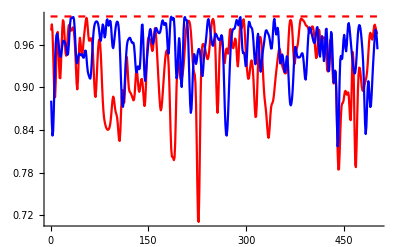

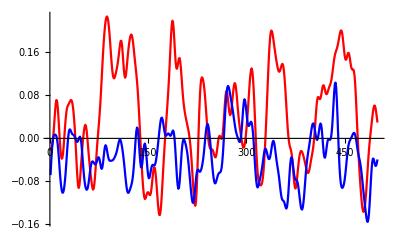

-Graphics-

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red}],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]

enexp=Conjugate[ψ].H[Ja,Jb,Jab,glist,glist].ψ//Chop;
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False,Epilog->{HalfLine[{enexp,0},{0,1}]}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
```

Plot for testing the proposal 3: [HA, HAB]!=0, [HB, HAB]!=0. x-x bond
A starts at the |uuuuu> but B with a random state
Note: 10 sites, NA=NB=5, JA=JB=JAB=1, g=0.5, θ=π/4
Run longer to t=50000 and see if thermalization occurs

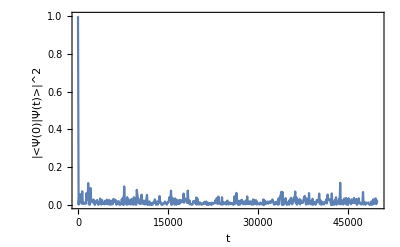

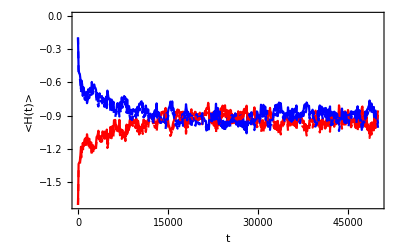

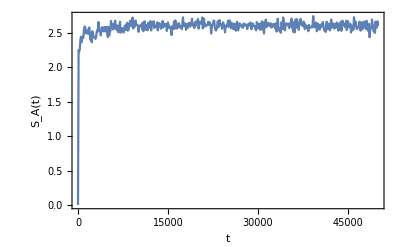

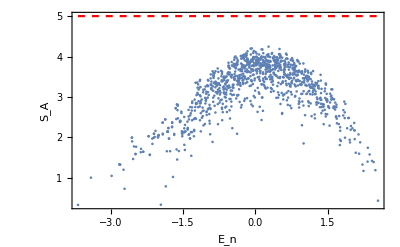

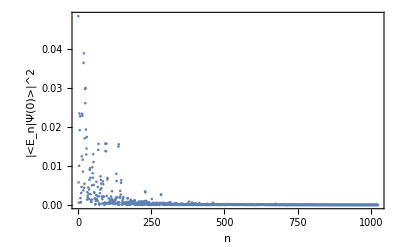

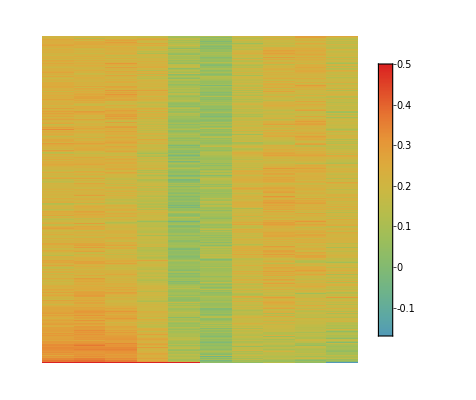

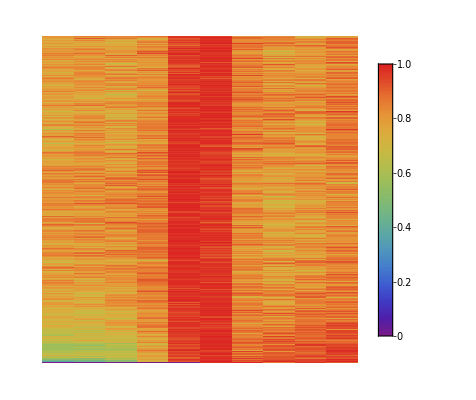

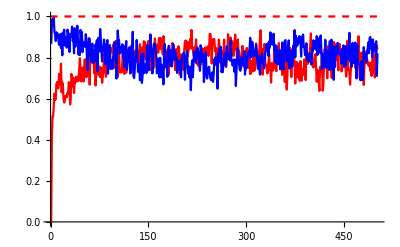

-Graphics-

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red},PlotRange->All],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]

enexp=Conjugate[ψ].H[Ja,Jb,Jab,glist,glist].ψ//Chop;
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False,Epilog->{HalfLine[{enexp,0},{0,1}]}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
```

Plot for testing the proposal 3: [HA, HAB]!=0, [HB, HAB]!=0.  
A starts at |uuuuu> but B with a random state
Note: 10 sites, NA=NB=5, JA=JB=1, JAB=1, g=0.5, θ=π/4
Run shorter to t=100 and see how thermalization starts

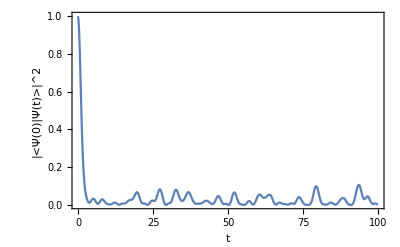

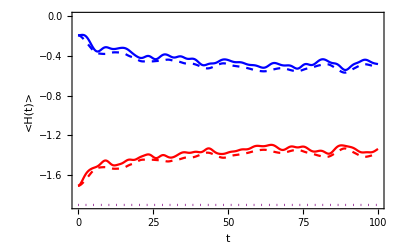

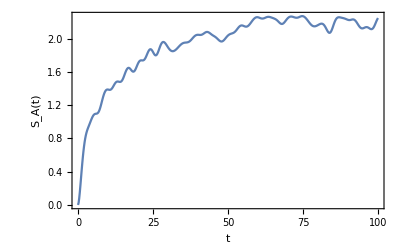

-Graphics-

-Graphics-

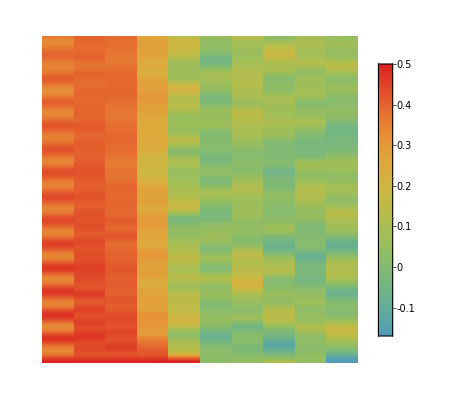

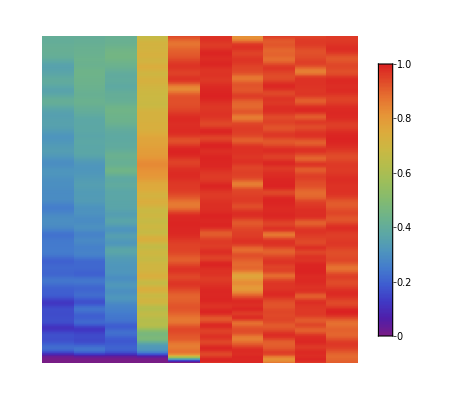

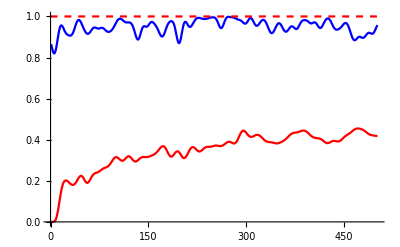

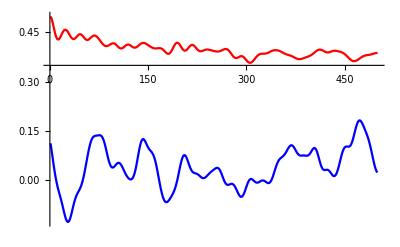

-Graphics-

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2,Hlist},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed},{Purple,Dotted}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red},PlotRange->All],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]

enexp=Conjugate[ψ].H[Ja,Jb,Jab,glist,glist].ψ//Chop;
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False,Epilog->{HalfLine[{enexp,0},{0,1}]}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
```

Plot for testing the proposal 3: [HA, HAB]!=0, [HB, HAB]!=0. x-x bond
A starts at the ground state but B with a random state
Note: 10 sites, NA=NB=5, JA=JB=JAB=1, g=0.5, θ=π/4
Run longer to t=10000 and see if thermalization occurs

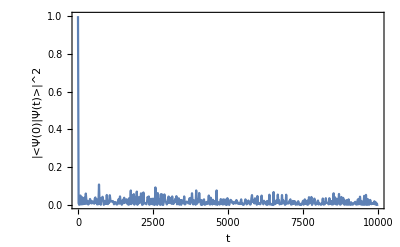

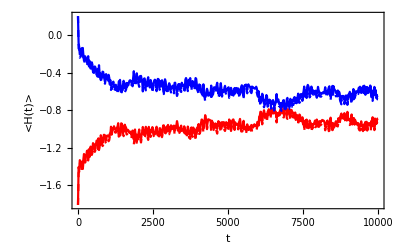

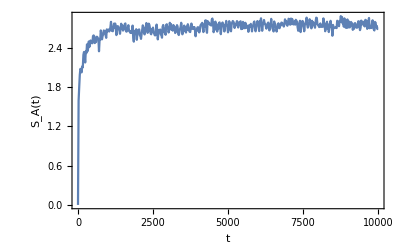

-Graphics-

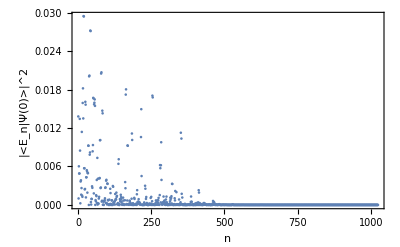

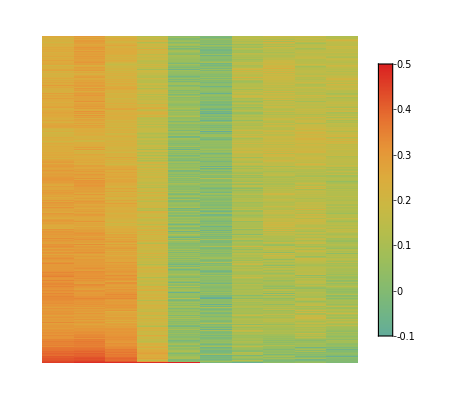

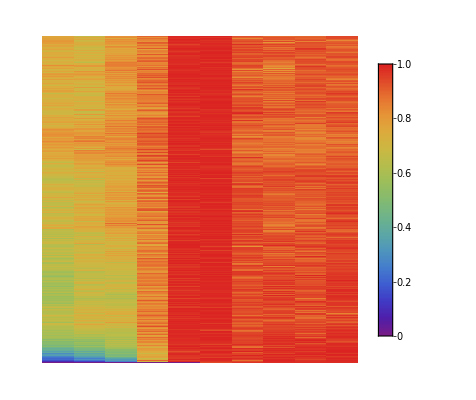

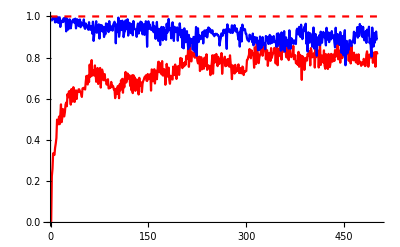

-Graphics-

-Graphics-

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red},PlotRange->All],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]

enexp=Conjugate[ψ].H[Ja,Jb,Jab,glist,glist].ψ//Chop;
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False,Epilog->{HalfLine[{enexp,0},{0,1}]}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
```

Plot for testing the proposal 3: [HA, HAB]!=0, [HB, HAB]!=0.  
A starts at ground state but B with a random state
Note: 10 sites, NA=NB=5, JA=JB=1, JAB=1, g=0.5, θ=π/4
Run shorter to t=500 and see how thermalization starts

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False]
ListPlot[{HAlist1,HBlist1,HAlist2,HBlist2,Hlist},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed},{Purple,Dotted}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False]
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

Show[ListPlot[Table[vNlist[[i,3]],{i,1,Dimensions[vNlist][[1]]}],Joined->True,AxesOrigin->{0,0},PlotStyle->{Red}],ListPlot[Table[vNlist[[i,8]],{i,1,Dimensions[vNlist][[1]]}],AxesOrigin->{0,0},Joined->True,PlotStyle->{Blue}],Plot[1,{x,0,Dimensions[vNlist][[1]]},PlotStyle->{Red,Dashed}],AxesOrigin->{0,0},PlotRange->All]

Show[ListPlot[Table[σlist[[i,3]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Red},PlotRange->All],ListPlot[Table[σlist[[i,8]],{i,2,Dimensions[σlist][[1]]}],Joined->True,PlotStyle->{Blue}],PlotRange->All]

enexp=Conjugate[ψ].H[Ja,Jb,Jab,glist,glist].ψ//Chop;
Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False,Epilog->{HalfLine[{enexp,0},{0,1}]}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»